Notebook with RVE
Notebook for Project 1
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# FEM Simulations

## Heterogeneous RVE

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Definition of Mesh, Loads and Boundary Conditions

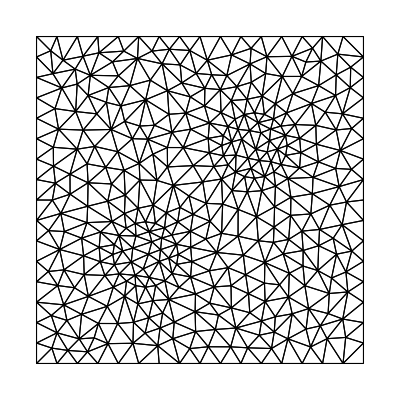

```mathematica
xc1=2/3;
yc1=2/3;
xc2=1/3;
yc2=1/3;
rincl = 1/10;
L=1;
q = 1000;

Ω=ImplicitRegion[(x-xc1)^2+(y-yc1)^2≥rincl^2&&(x-xc2)^2+(y-yc2)^2≥rincl^2,{{x,0,L},{y,0,L}}];
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->{{{L/100,L/100},1},{{xc1,yc1},2},{{xc2,yc2},3}},"MeshOrder"->1,"MaxBoundaryCellMeasure"->1];
%["Wireframe"]
```

```mathematica
(*Attention: the source AceGen code for T1LE (linear triangular elements) is missing - to be done*)
<<AceFEM`;
SMTInputData[];
SMTAddDomain[
{"T1 matrix","T1LE",{"E *"-> 1000,"ν *"->0.3}},
{"T1 inc 1","T1LE",{"E *"-> 10^6,"ν *"->0.3}},
{"T1 inc 2","T1LE",{"E *"-> 10^6,"ν *"->0.3}}
];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",{"T1",2}->"T1 inc 1",{"T1",3}->"T1 inc 2"}];
SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"D"],1-> 0, 2-> 0}];
SMTAddNaturalBoundary[Line[{{0,L},{L,L}},"D"],2->Line[{q}]];
SMTAnalysis[];
SMTShowMesh[]
```

-Graphics-

### Solution algorithm (one load-step, one NR iteration)

```mathematica
SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"]
```

False

```mathematica
Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]
]
```

-Graphics-